```mathematica
(*
Title: Homework 1 Simplification and Checking
Author: Jared Frazier
Course: Uncertainty Quantification 2023
*)

Clear["Global`*"]
On[Assert]
```

```mathematica
(*Exercise 1*)

(*Return the jacobi polynomial given α, β, and the polynomial order n

This function is from the wikipedia on Jacobi Polynomials*)
JacobiPolynomial[α_, β_, n_] := (
	∑_(s=0)^n (Binomial[n+α, n-s]*Binomial[n+β, s]*((x-1)/2)^s*((x+1)/2)^(n-s))
)

Assert[
	Simplify[Equal[(α + 1) + (α+β+2)*(x-1)/2, JacobiPolynomial[α, β, 1]]],
	"n = 1 jacobi polynomial matches wiki solution"
]

(*Parameters of weight function*)
α = 6;
β = 2;

(*Special cases of n = 0, 1, 2*)
P0 = JacobiPolynomial[α, β, 0];
P1 = JacobiPolynomial[α, β, 1];
P2 = JacobiPolynomial[α, β, 2];
myP = 28*((x+1)/2)^2+32*(x-1)/2*(x+1)/2+6((x-1)/2)^2; (*Hand computed*)
w = (1-x)^α*(1+x)^β; (*Weight function of beta distribution*)

Print["Simplification of P_2\n"]
Simplify[P2]
Simplify[myP]

(*How the Xiu ch. 3 shows you to compute the normalization constant γ*)
Print["Inner product w.r.t weight function w for n in [0..2]"]
P0InnerProduct = ∫_-1^1 P0^2*wⅆx
P1InnerProduct = ∫_-1^1 P1^2*wⅆx
P2InnerProduct = ∫_-1^1 P2^2*wⅆx

(*Return Subscript[γ, nm] , the normalization constant for the inner product of jacobi polynomials

This function is from the wikipedia on Jacobi Polynomials*)
JacobiNormalizationConstantGamma[α_, β_, n_] := (
	(2^(α+β+1))/(2*n+α+β+1)*(Gamma[n+α+1]*Gamma[n+β+1])/((Gamma[n+α+β+1])*n!)
)

Assert[
	JacobiNormalizationConstantGamma[α, β, 0] == P0InnerProduct,
	"closed form solution for n=0 jacobi normalization const matches 
	integrals solution"
]
Assert[
	JacobiNormalizationConstantGamma[α, β, 1] == P1InnerProduct,
	"closed form solution for n=1 jacobi normalization const matches 
	integrals solution"
]
Assert[
	JacobiNormalizationConstantGamma[α, β, 2] == P2InnerProduct,
	"closed form solution for n=2 jacobi normalization const matches 
	integrals solution"
]
```

Simplification of P_2

1/2 (1+22 x+33 x^2)

1/2 (1+22 x+33 x^2)

Inner product w.r.t weight function w for n in [0..2]

128/63

128/33

1024/195

```mathematica
(*Exercise 2: Polynomial Projection *)

(*Xiu 3.3.1 p. 31*)
InnerProductLP[u_, v_, I_] := NIntegrate[u * v, I] 
InnerProductNorm[u_, I_] := Sqrt[NIntegrate[u^2, I]]
FHatK[ϕ_, f_, I_] := (1/(InnerProductNorm[ϕ, I])^2)*InnerProductLP[f, ϕ, I] 
OrthogonalProjectionLP[N_, I_] := (
	∑_(k=0)^N (
	(*Evaluate the integrals for Subscript[f̂, k] in order to get the fourier coefficient*)
	  Subscript[f̂, k] = FHatK[LegendreP[k, t], Exp[2*t + Sin[4*t]], I];
      Subscript[ϕ, k] = LegendreP[k, x]; (*expression with x to be evaluated later*)
      Subscript[f̂, k] * Subscript[ϕ, k]
    )
)

projectionOnF = OrthogonalProjectionLP[7, {t, -1, 1}]; 

(*Plots of approximation function and truth function f*)
p1 = Plot[
    projectionOnF,
    {x, -1, 1},
    PlotStyle->Red,
    PlotRange->All,
    PlotLabels->"P_Nf(x)",
    ImageSize->Full];

p2 = Plot[
  Exp[2*t + Sin[4*t]], 
  {t, -1, 1},
  PlotRange->All, 
  ImageSize->Full,
  PlotLabels->"f(x)"];
  
Show[p1, p2]
```

-Graphics-

```mathematica
(*Computes approximatino error of projection*)
ApproximationError[projectionOnF_, I_] := Sqrt[
  NIntegrate[Abs[Exp[2*x + Sin[4*x]] - projectionOnF]^2, I]]
 
(*Compute approximation errors for desired order polynomial*)
errors = {};
For[k = 0, k <= 20, k++,
	errors = Append[
	  errors, 
	  ApproximationError[
	    OrthogonalProjectionLP[k, {t, -1, 1}],
	    {x, -1, 1}
	  ]
	]
]
```

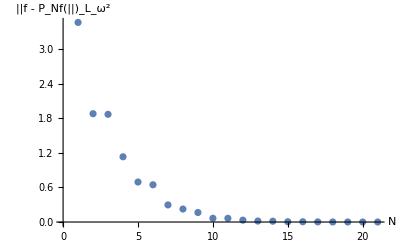

```mathematica
ListPlot[errors, AxesLabel->{"N", "||f - P_Nf(||)_(L_ω^2)"}, ImageSize->Full]
```

```mathematica
(*Exercise 2: Polynomial Interpolation
TODO: How to use the below expression as a function*)
Lagrange[x_, i_, N_] := ∏_(j=0)^N (If[i != j, (z - x[[j]])/(x[[i]] - x[[j]]), 1]) (*Careful with indices... this is probably not right*)
InterpolatingLagrangePolynomial[x_, y_, N_] := ∑_(i=0)^N (y[[i]]*Lagrange[x, i, N])
InterpolatingLagrangePolynomial[x, y, 3]; 

(*Generate some points using f(Subscript[x, i]) = Subscript[y, i] for {x ...} and {y...}
this will lead to a general formula that can be used to estimate on
the points*)
xs = Range[-1, 1, 0.1];
ys = Exp[2*xs + Sin[4*xs]];
```

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.